```mathematica
DSolve[{f'[x]==-1000f[x]+1000Sin[x]+Cos[x],f[0]== 1},f[x],x]
```

{{f[x]→ⅇ^(-1000 x) (1+ⅇ^(1000 x) Sin[x])}}

```mathematica
z[x_]:=ⅇ^(-1000 x)+Sin[x]
```

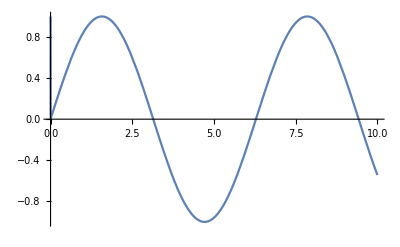

```mathematica
Plot[z[x], {x,0,10}]
```